```mathematica
eminobsMeV=0.1;
(*eminobsMeV=1.0; *)
eminobs=eminobsMeV*ergPmev/(me*c^2); (* most strict lower-limit for highest-energy photon *)
epmin=eminobs/gammavalue;
alphasp=2.00001; (* shocks? *) (* for exactly 2, choose something like 2.00001 so don't have to worry about ensuring mathematica integrated to get general solution that allows log version when \alpha=2 *)
Area=Pi*Rjet*Lpnum;
deltat=Ttransit;
```

```mathematica
epmin
```

0.000516919

```mathematica
taugtot[.001,epmin/10,1,1]
```

0.936432

```mathematica
sigmagg[2.001]/sigmat
```

0.0610705

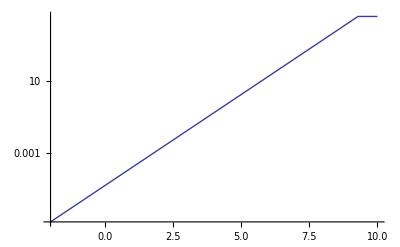

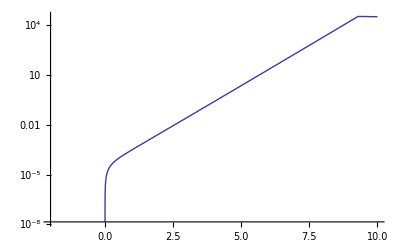

```mathematica
LogPlot[taugg[10^lx,epmin/10^6,10^10],{lx,-2,10}]
LogPlot[taugg[10^lx,epmin/10^6,10^lx],{lx,-2,10}]
```

```mathematica
pickep=10^8;
epmax=10^8;
epthick=1;
epminpick=10^(-8);
Print["taus"];
taugg[pickep,epminpick,epmax]
tauggge[pickep,epminpick,epmax,epthick]
tauge[pickep]
```

taus

2094.99

2.52103×10^-11

6.9014×10^-8

```mathematica
Plot3D[Log[10,taugtot[10^lx,10^(-20),10^lx,10^ly]],{lx,-2,8},{ly,-2,8}]
```

$Aborted

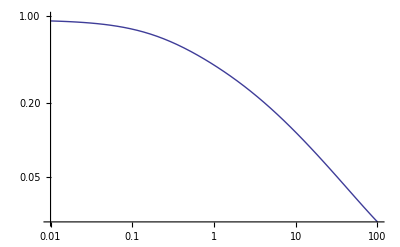

```mathematica
LogLogPlot[taugtot[x,10^(-20),x,1],{x,0.01,100}]
```

```mathematica
eminobsMeV=0.1;
(*eminobsMeV=1.0; *)
eminobs=eminobsMeV*ergPmev/(me*c^2); (* most strict lower-limit for highest-energy photon *)
epmin=eminobs/gammavalue;
alphasp=2.00001; (* shocks? *) (* for exactly 2, choose something like 2.00001 so don't have to worry about ensuring mathematica integrated to get general solution that allows log version when \alpha=2 *)
Area=Pi*Rjet*Lpnum;
deltat=Ttransit;
```

```mathematica
p1=ContourPlot[taugtot[10^lepmax,epmin/10^8,10^lepmax,10^lepthick]==1,{lepmax,-2,10},{lepthick,-2,10}];
p2=ContourPlot[taugg[10^lepthick,epmin/10^8,10^lepmax]==1,{lepmax,-2,10},{lepthick,-2,10}];
minelement[p1,p2]
```

{{5.33291,5.33291},0.0000113284,140,87,229,245,{5.3329,5.3329},{5.33291,5.33291}}

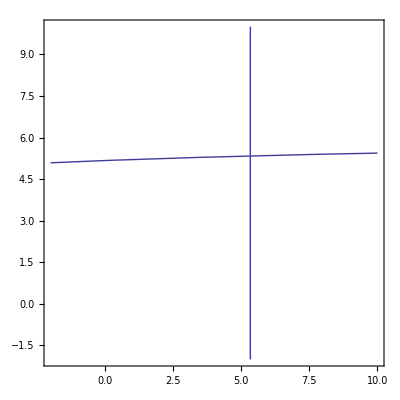

```mathematica
Show[{p1,p2}]
```

```mathematica
{epmaxerror,epmaxnum,epthicknum,epmaxobs,epmaxminerror,epmaxminnum,epmaxminobs,epmaxmaxerror,epmaxmaxnum,epmaxmaxobs}=tauhighe;
```

```mathematica
{epmaxerror,epmaxnum,epthicknum,epmaxobs,epmaxminerror,epmaxminnum,epmaxminobs,epmaxmaxerror,epmaxmaxnum,epmaxmaxobs}
```

{epmaxerror$1630826,epmaxnum$1630826,epthicknum$1630826,361.58061673934689726830448288 epmaxnum$1630826,epmaxminerror$1630826,epmaxminnum$1630826,361.58061673934689726830448288 epmaxminnum$1630826,epmaxmaxerror$1630826,epmaxmaxnum$1630826,361.58061673934689726830448288 epmaxmaxnum$1630826}

```mathematica
ContourPlot[tauhighe[x,10^ly][[2]],{x,2.001,3},{ly,Log[10,10^(-8)],Log[10,0.1]},Contours->3]
```

minmethodtau=3

CP1

CP2

CPdone

solsTtrial={epmax→201913.772913150896783918142319,epthick→201913.772913150896783918142319}

errorTnpairs=0

minmethodtau=3

CP1

CP2

CPdone

ContourPlot+FindRoot failed min=100000000000000000000

minmethodtau=3

CP1

$Aborted

((2.001
1.×10^-8) | (2.001
3.98107×10^-7) | (2.001
0.0000158489) | (2.001
0.000630957) | (2.001
0.0251189)
(2.2008
1.×10^-8) | (2.2008
3.98107×10^-7) | (2.2008
0.0000158489) | (2.2008
0.000630957) | (2.2008
0.0251189)
(2.4006
1.×10^-8) | (2.4006
3.98107×10^-7) | (2.4006
0.0000158489) | (2.4006
0.000630957) | (2.4006
0.0251189)
(2.6004
1.×10^-8) | (2.6004
3.98107×10^-7) | (2.6004
0.0000158489) | (2.6004
0.000630957) | (2.6004
0.0251189)
(2.8002
1.×10^-8) | (2.8002
3.98107×10^-7) | (2.8002
0.0000158489) | (2.8002
0.000630957) | (2.8002
0.0251189))

```mathematica
tautable=Table[tauhighe[taux[ii,numi],tauy[jj,numj]][[4]],{ii,0,numi},{jj,0,numj}];
```

minmethodtau=3

CP1

CP2

CPdone

Trial here 1.35551×10^7 2.22648×10^7

solsTtrial={epmax→1.35551×10^7,epthick→2.22648×10^7}

errorTnpairs=1/10000000000000000000000000

minmethodtau=3

CP1

CP2

CPdone

Trial here 1.35513×10^7 2.22618×10^7

solsTtrial={epmax→1.35513×10^7,epthick→2.22618×10^7}

errorTnpairs=1/10000000000000000000000000

minmethodtau=3

CP1

CP2

CPdone

Trial here 1.35435×10^7 2.22555×10^7

solsTtrial={epmax→1.35435×10^7,epthick→2.22555×10^7}

errorTnpairs=1/10000000000000000000000000

minmethodtau=3

CP1

CP2

CPdone

Trial here 1.35402×10^7 2.22171×10^7

solsTtrial={epmax→1.35402×10^7,epthick→2.22171×10^7}

errorTnpairs=1/10000000000000000000000000

minmethodtau=3

CP1

CP2

CPdone

ContourPlot+FindRoot failed min=100000000000000000000

minmethodtau=3

CP1

CP2

CPdone

ContourPlot+FindRoot failed min=100000000000000000000

minmethodtau=3

CP1

CP2

CPdone

Trial here 222810. 256527.

solsTtrial={epmax→222810.,epthick→256527.}

errorTnpairs=1/10000000000000000000000000

minmethodtau=3

CP1

CP2

CPdone

Trial here 202414. 234576.

solsTtrial={epmax→202414.,epthick→234576.}

errorTnpairs=1/10000000000000000000000000

minmethodtau=3

CP1

CP2

CPdone

Trial here 181150. 214964.

solsTtrial={epmax→181150.,epthick→214964.}

errorTnpairs=1/10000000000000000000000000

minmethodtau=3

CP1

CP2

CPdone

Trial here 159556. 194175.

solsTtrial={epmax→159556.,epthick→194175.}

errorTnpairs=1/10000000000000000000000000

minmethodtau=3

CP1

CP2

CPdone

Trial here 138526. 173979.

solsTtrial={epmax→138526.,epthick→173979.}

errorTnpairs=1/10000000000000000000000000

minmethodtau=3

CP1

CP2

CPdone

ContourPlot+FindRoot failed min=100000000000000000000

minmethodtau=3

CP1

CP2

CPdone

Trial here 705488. 705586.

solsTtrial={epmax→705488.,epthick→705586.}

errorTnpairs=1/10000000000000000000000000

minmethodtau=3

CP1

CP2

CPdone

Trial here 377997. 378119.

solsTtrial={epmax→377997.,epthick→378119.}

errorTnpairs=1/10000000000000000000000000

minmethodtau=3

CP1

CP2

CPdone

Trial here 205580. 205758.

solsTtrial={epmax→205580.,epthick→205758.}

errorTnpairs=1/10000000000000000000000000

minmethodtau=3

CP1

CP2

CPdone

Trial here 110847. 111083.

solsTtrial={epmax→110847.,epthick→111083.}

errorTnpairs=1/10000000000000000000000000

minmethodtau=3

CP1

CP2

CPdone

Trial here 59528.4 59866.4

solsTtrial={epmax→59528.4,epthick→59866.4}

errorTnpairs=1/10000000000000000000000000

minmethodtau=3

CP1

CP2

CPdone

ContourPlot+FindRoot failed min=100000000000000000000

minmethodtau=3

CP1

CP2

CPdone

Trial here 4.19758×10^6 4.19758×10^6

solsTtrial={epmax→4.19758×10^6,epthick→4.19758×10^6}

errorTnpairs=1/10000000000000000000000000

minmethodtau=3

CP1

CP2

CPdone

Trial here 1.46941×10^6 1.46941×10^6

solsTtrial={epmax→1.46941×10^6,epthick→1.46941×10^6}

errorTnpairs=1/10000000000000000000000000

minmethodtau=3

CP1

CP2

CPdone

Trial here 512137. 512140.

solsTtrial={epmax→512137.,epthick→512140.}

errorTnpairs=1/10000000000000000000000000

minmethodtau=3

CP1

CP2

CPdone

Trial here 178512. 178516.

solsTtrial={epmax→178512.,epthick→178516.}

errorTnpairs=1/10000000000000000000000000

minmethodtau=3

CP1

CP2

CPdone

Trial here 62275. 62279.7

solsTtrial={epmax→62275.,epthick→62279.7}

errorTnpairs=1/10000000000000000000000000

minmethodtau=3

CP1

CP2

CPdone

ContourPlot+FindRoot failed min=100000000000000000000

minmethodtau=3

CP1

CP2

CPdone

Trial here 1.88647×10^7 1.88647×10^7

solsTtrial={epmax→1.88647×10^7,epthick→1.88647×10^7}

errorTnpairs=1/10000000000000000000000000

minmethodtau=3

CP1

CP2

CPdone

Trial here 4.72909×10^6 4.72909×10^6

solsTtrial={epmax→4.72909×10^6,epthick→4.72909×10^6}

errorTnpairs=1/10000000000000000000000000

minmethodtau=3

CP1

CP2

CPdone

Trial here 1.19843×10^6 1.19843×10^6

solsTtrial={epmax→1.19843×10^6,epthick→1.19843×10^6}

errorTnpairs=1/10000000000000000000000000

minmethodtau=3

CP1

CP2

CPdone

Trial here 301096. 301098.

solsTtrial={epmax→301096.,epthick→301098.}

errorTnpairs=1/10000000000000000000000000

minmethodtau=3

CP1

CP2

CPdone

Trial here 75457.8 75460.1

solsTtrial={epmax→75457.8,epthick→75460.1}

errorTnpairs=1/10000000000000000000000000

minmethodtau=3

CP1

CP2

CPdone

ContourPlot+FindRoot failed min=100000000000000000000

minmethodtau=3

CP1

CP2

CPdone

Trial here 6.47225×10^7 6.47225×10^7

solsTtrial={epmax→6.47225×10^7,epthick→6.47225×10^7}

errorTnpairs=1/10000000000000000000000000

minmethodtau=3

CP1

CP2

CPdone

Trial here 1.24627×10^7 1.24627×10^7

solsTtrial={epmax→1.24627×10^7,epthick→1.24627×10^7}

errorTnpairs=1/10000000000000000000000000

minmethodtau=3

CP1

CP2

CPdone

Trial here 2.45371×10^6 2.45371×10^6

solsTtrial={epmax→2.45371×10^6,epthick→2.45371×10^6}

errorTnpairs=1/10000000000000000000000000

minmethodtau=3

CP1

CP2

CPdone

Trial here 475975. 475978.

solsTtrial={epmax→475975.,epthick→475978.}

errorTnpairs=1/10000000000000000000000000

minmethodtau=3

CP1

CP2

CPdone

Trial here 91738.4 91740.6

solsTtrial={epmax→91738.4,epthick→91740.6}

errorTnpairs=1/10000000000000000000000000

minmethodtau=3

CP1

CP2

CPdone

ContourPlot+FindRoot failed min=100000000000000000000

```mathematica
MatrixForm[tautable]
```

(4.90127×10^9 | 4.8999×10^9 | 4.89707×10^9 | 4.89587×10^9 | 0 | 0
8.05636×10^7 | 7.31891×10^7 | 6.55004×10^7 | 5.76922×10^7 | 5.00885×10^7 | 0
2.55091×10^8 | 1.36676×10^8 | 7.43336×10^7 | 4.008×10^7 | 2.15243×10^7 | 0
1.51776×10^9 | 5.3131×10^8 | 1.85179×10^8 | 6.45466×10^7 | 2.25174×10^7 | 0
6.82111×10^9 | 1.70995×10^9 | 4.33329×10^8 | 1.0887×10^8 | 2.72841×10^7 | 0
2.34024×10^10 | 4.50627×10^9 | 8.87213×10^8 | 1.72103×10^8 | 3.31708×10^7 | 0)

```mathematica
tauhighe[2.00001,10^(-6)*gammavalue]
```

minmethodtau=3

CP1

CP2

CPdone

Trial here 139209. 175593.

solsTtrial={epmax→139209.,epthick→175593.}

errorTnpairs=1/10000000000000000000000000

{1/10000000000000000000000000,139209.,175593.,5.03352×10^7,1000000000000000000000000000000,0,0,1000000000000000000000000000000,0,0}

```mathematica
myepmax=10^(5.5);
myepmin=10^(-6);
taugg[myepmax,myepmin,myepmax*10000]
```

1.58983

```mathematica
Nee[10^(-6),10^6,10^5]
```

8.44812×10^39

```mathematica
taugg[10^5.5,10^(-6),10^6]
```

2.05344

```mathematica
taugg[10^(5.128),10^(-6),10^6]
```

0.871925

```mathematica
epmin
```

0.000276563

```mathematica
Nee[10^(-6),10^6,10^5]
```

8.44812×10^39

```mathematica
tauggge[10^6,10^(-6),10^6,10]
```

5.97955×10^-11

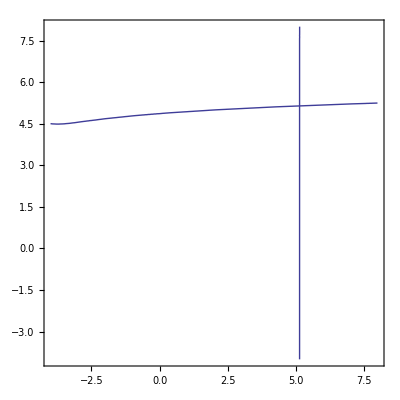

```mathematica
Show[{p1globaltau,p2globaltau}]
```

```mathematica
Dimensions[p1globaltau[[1,1]]][[1]]
```

182

```mathematica
epmaxes=Table[p1globaltau[[1,1,ii,1]],{ii,1,Dimensions[p1globaltau[[1,1]]][[1]]}];
Max[epmaxes]
```

-3.46646

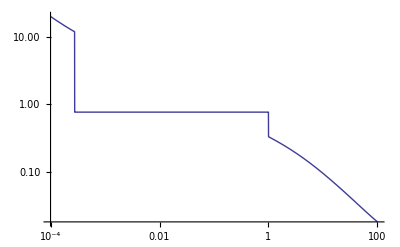

```mathematica
LogLogPlot[taugtot[x,0.00027656349751758715,x,1],{x,0.0001,100}]
```

```mathematica
sigmage[0.00001]
```

6.65077303830217264450231561×10^-25

```mathematica
tauge1[.01]
```

0.761302

```mathematica
sigmaesnum/sigmaknnum
```

1.

```mathematica
mysigmakn
```

0.75 (-(1+3 ep)/(1+2 ep)^2+Log[1+2 ep]/(2 ep)+((1+ep) ((2 (1+ep))/(1+2 ep)-Log[1+2 ep]/ep))/ep^2)

```mathematica
sigmage[10^8]
```

4.89176683856605763189545353×10^-32

```mathematica
mysigmakn//.{ep->0.0000000001}
```

-1.24111×10^13

```mathematica
sigmaknnew//.{alphakn->2.0001}
```

2.08906×10^-25

```mathematica
sigmaknnew//.{alphakn->
```

4.988079778726629483376736708×10^-25 (-(1+3 alphakn)/(1+2 alphakn)^2+Log[1+2 alphakn]/(2 alphakn)+((1+alphakn) ((2 (1+alphakn))/(1+2 alphakn)-Log[1+2 alphakn]/alphakn))/alphakn^2)

```mathematica
sigmakngen//.{freqgamma->0.0000000000000001}
```

1.52304×10^48

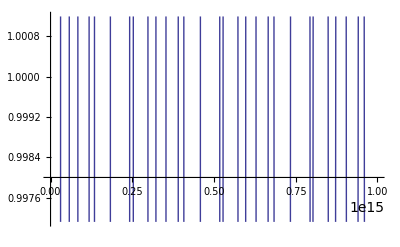

```mathematica
Plot[sigmakngen/sigmat,{freqgamma,0,10^17}]
```

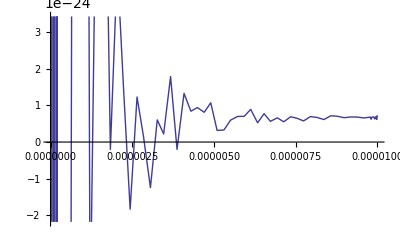

```mathematica
Plot[(2*Pi*q^4)/(me^2*c^4)*((1+alphakn)/(alphakn^2)*(2*(1+alphakn)/(1+2*alphakn)-1/alphakn*Log[1+2*alphakn])+1/(2*alphakn)*Log[1+2*alphakn]-(1+3*alphakn)/(1+2*alphakn)^2),{alphakn,0,10^(-5)}]
```